Reorganización de listas

Muchas veces se quiere reorganizar una lista que se haya generado en algún proceso, antes de poder utilizarla en otro. Por ejemplo, puede tenerse una lista de pares que se necesite convertir a un par de listas, o viceversa.

Transponga una lista de pares para convertirla en un par de listas:

```mathematica
Transpose[{{1,2},{3,4},{5,6},{7,8},{9,10}}]
```

{{1,3,5,7,9},{2,4,6,8,10}}

Transponga de nuevo el par de listas para obtener una lista de pares:

```mathematica
Transpose[{{1,3,5,7,9},{2,4,6,8,10}}]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

Thread es una operación estrechamente relacionada con la anterior, que sirve, entre otras, para generar una entrada para Graph.

“Enhebrar” → a través de los elementos de dos listas:

```mathematica
Thread[{1,3,5,7,9}->{2,4,6,8,10}]
```

{1→2,3→4,5→6,7→8,9→10}

Partition toma una lista y la particiona en bloques de un tamaño especificado.

Particione una lista con 12 elementos en bloques de tamaño 3:

```mathematica
Partition[Range[12],3]
```

{{1,2,3},{4,5,6},{7,8,9},{10,11,12}}

Particione una lista de caracteres y mostrarlos en una rejilla:

```mathematica
Grid[Partition[Characters["An array of text made in the Wolfram Language"],9],Frame->All]
```

A | n |   | a | r | r | a | y |  
o | f |   | t | e | x | t |   | m
a | d | e |   | i | n |   | t | h
e |   | W | o | l | f | r | a | m
  | L | a | n | g | u | a | g | e

Si no se especifica lo contrario, Partition descompone una lista en bloques que no se traslapen. Sin embargo, puede pedirse que la lista se descomponga en bloques que permitan un traslape mediante un desplazamiento especificado en la lista.

Particione una lista en bloques de tamaño 3, con un desplazamiento de 1:

```mathematica
Partition[Range[10],3,1]
```

{{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{8,9,10}}

Particione una lista de caracteres en bloques con un desplazamiento de 1:

```mathematica
Grid[Partition[Characters["Wolfram Language"],12,1],Frame->All]
```

W | o | l | f | r | a | m |   | L | a | n | g
o | l | f | r | a | m |   | L | a | n | g | u
l | f | r | a | m |   | L | a | n | g | u | a
f | r | a | m |   | L | a | n | g | u | a | g
r | a | m |   | L | a | n | g | u | a | g | e

En vez de lo anterior, use un desplazamiento de 2:

```mathematica
Grid[Partition[Characters["Wolfram Language"],12,2],Frame->All]
```

W | o | l | f | r | a | m |   | L | a | n | g
l | f | r | a | m |   | L | a | n | g | u | a
r | a | m |   | L | a | n | g | u | a | g | e

Partition toma una lista y la descompone en sublistas. Flatten “aplana” las sublistas.

Forme una lista de las listas de los dígitos de enteros consecutivos:

```mathematica
IntegerDigits/@Range[20]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{1,0},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{2,0}}

Obtenga la versión aplanada:

```mathematica
Flatten[IntegerDigits/@Range[20]]
```

{1,2,3,4,5,6,7,8,9,1,0,1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,2,0}

Produzca un gráfico con la secuencia de dígitos:

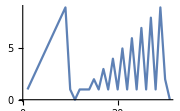

```mathematica
ListLinePlot[Flatten[IntegerDigits/@Range[20]]]
```

Normalmente, Flatten aplana en todos los niveles de una lista. Sin embargo, muchas veces se querría aplanar, por ejemplo, solo un nivel de la lista. Aquí se forma una tabla de 4×4, donde cada elemento es, a su vez, una lista.

Forme una lista de listas de listas:

```mathematica
Table[IntegerDigits[i^j],{i,4},{j,4}]
```

{{{1},{1},{1},{1}},{{2},{4},{8},{1,6}},{{3},{9},{2,7},{8,1}},{{4},{1,6},{6,4},{2,5,6}}}

Aplane todo el resultado:

```mathematica
Flatten[Table[IntegerDigits[i^j],{i,4},{j,4}]]
```

{1,1,1,1,2,4,8,1,6,3,9,2,7,8,1,4,1,6,6,4,2,5,6}

Aplane solo un nivel de la lista:

```mathematica
Flatten[Table[IntegerDigits[i^j],{i,4},{j,4}],1]
```

{{1},{1},{1},{1},{2},{4},{8},{1,6},{3},{9},{2,7},{8,1},{4},{1,6},{6,4},{2,5,6}}

ArrayFlatten es una generalización de Flatten, que toma arreglos de arreglos y los aplana para hacer arreglos individuales.

Aquí se genera una estructura con anidación profunda que resulta difícil de comprender:

```mathematica
NestList[{{#,0},{#,#}}&,{{1}},2]
```

{{{1}},{{{{1}},0},{{{1}},{{1}}}},{{{{{{1}},0},{{{1}},{{1}}}},0},{{{{{1}},0},{{{1}},{{1}}}},{{{{1}},0},{{{1}},{{1}}}}}}}

ArrayFlatten la convierte en una estructura un poco más fácil de entender:

```mathematica
NestList[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},2]
```

{{{1}},{{1,0},{1,1}},{{1,0,0,0},{1,1,0,0},{1,0,1,0},{1,1,1,1}}}

Con ArrayPlot, es considerablemente más sencillo darse cuenta de lo que está sucediendo:

```mathematica
ArrayPlot/@NestList[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Genere un patrón de Sierpinski fractal con 8 niveles de anidación:

```mathematica
ArrayPlot[Nest[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},8]]
```

-Graphics-

Hay muchas otras maneras de reorganizar listas. Por ejemplo, Split subdivide una lista en secuencias de elementos idénticos.

Subdivida una lista en secuencias de elementos idénticos consecutivos:

```mathematica
Split[{1,1,1,2,2,1,1,3,1,1,1,2}]
```

{{1,1,1},{2,2},{1,1},{3},{1,1,1},{2}}

Gather, por otro lado, agrupa los elementos que sean idénticos, dondequiera que éstos aparezcan.

Agrupe en listas los elementos idénticos:

```mathematica
Gather[{1,1,1,2,2,1,1,3,1,1,1,2}]
```

{{1,1,1,1,1,1,1,1},{2,2,2},{3}}

GatherBy agrupa los elementos según el resultado de aplicar una función a cada uno. Ahora, se usa LetterQ, de modo tal que agrupa por separado los caracteres que son letras y los que no lo son.

Agrupe los caracteres según sean letras o no lo sean:

```mathematica
GatherBy[Characters["It's true that 2+2 is equal to 4!"],LetterQ]
```

{{I,t,s,t,r,u,e,t,h,a,t,i,s,e,q,u,a,l,t,o},{', , , ,2,+,2, , , , ,4,!}}

SortBy ordena según el resultado de aplicar una función.

Sort normalmente ordena las listas cortas antes de las más largas:

```mathematica
Sort[Table[IntegerDigits[2^n],{n,10}]]
```

{{2},{4},{8},{1,6},{3,2},{6,4},{1,2,8},{2,5,6},{5,1,2},{1,0,2,4}}

Ahora se le pide a SortBy que haga el ordenamiento de acuerdo al primer elemento de cada lista:

```mathematica
SortBy[Table[IntegerDigits[2^n],{n,10}],First]
```

{{1,6},{1,2,8},{1,0,2,4},{2},{2,5,6},{3,2},{4},{5,1,2},{6,4},{8}}

Sort ordena una lista. Union, además, elimina los elementos repetidos.

Encuentre en una lista todos los elementos que sean distintos:

```mathematica
Union[{1,9,5,3,1,4,3,1,3,3,5,3,9}]
```

{1,3,4,5,9}

Se puede usar Union para encontrar la “unión” de los elementos que aparezcan en cualesquiera de varias listas.

Obtenga la lista de todos los elementos que aparezcan en cualquiera de las listas:

```mathematica
Union[{2,1,3,7,9},{4,5,1,2,3,3},{3,1,2,8,5}]
```

{1,2,3,4,5,7,8,9}

Encuentre los elementos que sean comunes a todas las listas:

```mathematica
Intersection[{2,1,3,7,9},{4,5,1,2,3,3},{3,1,2,8}]
```

{1,2,3}

Encuentre los elementos que estén en la primera de las listas, pero no en la segunda:

```mathematica
Complement[{4,5,1,2,3,3},{3,1,2,8}]
```

{4,5}

Encuentre las letras que aparezcan en cualquiera de los alfabetos inglés, sueco o turco:

```mathematica
Union[Alphabet["English"],Alphabet["Swedish"],Alphabet["Turkish"]]
```

{ğ,ş,a,å,ä,b,c,ç,d,e,f,g,h,i,ı,j,k,l,m,n,o,ö,p,q,r,s,t,u,ü,v,w,x,y,z}

Las letras que aparecen en el sueco, pero no en el inglés:

```mathematica
Complement[Alphabet["Swedish"],Alphabet["English"]]
```

{å,ä,ö}

Otra de las muchas funciones que se pueden aplicar a las listas es Riffle, que intercala cosas entre los elementos sucesivos de una lista.

Intercale x entre los elementos de una lista:

```mathematica
Riffle[{1,2,3,4,5},x]
```

{1,x,2,x,3,x,4,x,5}

Intercale -- entre una lista de caracteres:

```mathematica
Riffle[Characters["WOLFRAM"],"--"]
```

{W,--,O,--,L,--,F,--,R,--,A,--,M}

Junte todo lo anterior en una sola lista de caracteres:

```mathematica
StringJoin[Riffle[Characters["WOLFRAM"],"--"]]
```

W--O--L--F--R--A--M

Las funciones tales como Partition sirven para tomar una lista y descomponerla en sublistas. En vez de eso, a veces se parte de una colección de elementos para formar listas con ellos.

Permutations obtiene todos los ordenamientos posibles, o permutaciones, de una lista.

Genere una lista de los 3!=3×2×1=6 ordenamientos posibles de 3 elementos:

```mathematica
Permutations[{Red,Green,Blue}]
```

{{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0]},{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0, 0]}}

Genere todos los 2^3=8 subconjuntos que se pueden formar con los elementos de una lista de 3:

```mathematica
Subsets[{Red,Green,Blue}]
```

{{},{RGBColor[1, 0, 0]},{RGBColor[0, 1, 0]},{RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}}

Tuples toma una lista de elementos y genera todas las combinaciones posibles de un número dado de dichos elementos.

Genere una lista de todas las ternas posibles de rojo y verde:

```mathematica
Tuples[{Red,Green},3]
```

{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0]},{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]}}

RandomChoice sirve para hacer una elección aleatoria a partir de los elementos de una lista.

Haga una elección aleatoria a partir de los elementos de una lista:

```mathematica
RandomChoice[{Red,Green,Blue}]
```

RGBColor[0, 1, 0]

Haga una lista de 20 elecciones aleatorias:

```mathematica
RandomChoice[{Red,Green,Blue},20]
```

{RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}

Haga 5 listas de 3 elecciones aleatorias:

```mathematica
RandomChoice[{Red,Green,Blue},{5,3}]
```

{{RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0]}}

RandomSample obtiene una muestra aleatoria de elementos de una lista, sin seleccionar más de una vez ningún elemento.

Elija 20 elementos en el tramo de 1 a 100, sin que aparezca ningún elemento repetido:

```mathematica
RandomSample[Range[100],20]
```

{82,3,93,92,39,45,63,32,79,75,34,1,11,59,98,67,38,44,28,76}

Si no se indica cuántos elementos se han de elegir, se obtiene un ordenamiento aleatorio de la lista completa:

```mathematica
RandomSample[Range[10]]
```

{2,5,1,7,4,6,3,8,9,10}

Vocabulario

Transpose[lista] |   | transpone las listas interior y exterior
Thread[lista_1→lista_2] |   | enhebra a través de elementos de listas 
Partition[lista,n] |   | particiona en bloques de tamaño n 
Flatten[lista] |   | aplana todas las sublistas 
Flatten[lista,k] |   | aplana k niveles de las sublistas 
ArrayFlatten[lista] |   | aplana arreglos de arreglos 
Split[lista] |   | separa en secuencias de elementos idénticos 
Gather[lista] |   | agrupa en listas los elementos idénticos 
GatherBy[lista,f] |   | agrupa de acuerdo con el resultado de aplicar f 
SortBy[lista,f] |   | ordena de acuerdo con el resultado de aplicar f  
Riffle[lista,x] |   | intercala x entre los elementos de lista 
Union[lista] |   | los elementos diferentes en lista
Union[lista_1,lista_2, ...] |   | los elementos que aparecen en cualquiera de las listas
Intersection[lista_1,lista_2, ...] |   | los elementos que aparecen en todas las listas
Complement[lista_1,lista_2] |   | los elementos que aparecen en lista_1 pero no en lista_2
Permutations[lista] |   | todas las permutaciones (ordenamientos) posibles 
Subsets[lista] |   | todos los subconjuntos posibles 
Tuples[lista,n] |   | todas las combinaciones posibles de n elementos 
RandomChoice[lista] |   | elige aleatoriamente dentro de una lista 
RandomChoice[lista,n] |   | n elecciones aleatorias 
RandomSample[lista,n] |   | n muestras aleatorias sin repeticiones 
RandomSample[lista] |   | ordenamiento aleatorio de una lista

"21 Exercises Available"
"with 13 extras" | "Get Started »"

Use Thread para formar una lista de reglas que liguen cada letra del alfabeto inglés con su posición en el alfabeto. »

| Expected output: |  
  | {"a"→1,"b"→2,"c"→3,"d"→4,"e"→5,"f"→6,"g"→7,"h"→8,"i"→9,"j"→10,"k"→11,"l"→12,"m"→13,"n"→14,"o"→15,"p"→16,"q"→17,"r"→18,"s"→19,"t"→20,"u"→21,"v"→22,"w"→23,"x"→24,"y"→25,"z"→26} |

Haga una rejilla de 4×6 con las 24 primeras letras del alfabeto inglés. »

| Expected output: |  
  | "a" | "b" | "c" | "d" | "e" | "f"
"g" | "h" | "i" | "j" | "k" | "l"
"m" | "n" | "o" | "p" | "q" | "r"
"s" | "t" | "u" | "v" | "w" | "x" |

Forme una rejilla con los dígitos en 2^1000, con 50 dígitos en cada renglón y con un marco en todos los casos. »

| Expected output: |  
  | 1 | 0 | 7 | 1 | 5 | 0 | 8 | 6 | 0 | 7 | 1 | 8 | 6 | 2 | 6 | 7 | 3 | 2 | 0 | 9 | 4 | 8 | 4 | 2 | 5 | 0 | 4 | 9 | 0 | 6 | 0 | 0 | 0 | 1 | 8 | 1 | 0 | 5 | 6 | 1 | 4 | 0 | 4 | 8 | 1 | 1 | 7 | 0 | 5 | 5
3 | 3 | 6 | 0 | 7 | 4 | 4 | 3 | 7 | 5 | 0 | 3 | 8 | 8 | 3 | 7 | 0 | 3 | 5 | 1 | 0 | 5 | 1 | 1 | 2 | 4 | 9 | 3 | 6 | 1 | 2 | 2 | 4 | 9 | 3 | 1 | 9 | 8 | 3 | 7 | 8 | 8 | 1 | 5 | 6 | 9 | 5 | 8 | 5 | 8
1 | 2 | 7 | 5 | 9 | 4 | 6 | 7 | 2 | 9 | 1 | 7 | 5 | 5 | 3 | 1 | 4 | 6 | 8 | 2 | 5 | 1 | 8 | 7 | 1 | 4 | 5 | 2 | 8 | 5 | 6 | 9 | 2 | 3 | 1 | 4 | 0 | 4 | 3 | 5 | 9 | 8 | 4 | 5 | 7 | 7 | 5 | 7 | 4 | 6
9 | 8 | 5 | 7 | 4 | 8 | 0 | 3 | 9 | 3 | 4 | 5 | 6 | 7 | 7 | 7 | 4 | 8 | 2 | 4 | 2 | 3 | 0 | 9 | 8 | 5 | 4 | 2 | 1 | 0 | 7 | 4 | 6 | 0 | 5 | 0 | 6 | 2 | 3 | 7 | 1 | 1 | 4 | 1 | 8 | 7 | 7 | 9 | 5 | 4
1 | 8 | 2 | 1 | 5 | 3 | 0 | 4 | 6 | 4 | 7 | 4 | 9 | 8 | 3 | 5 | 8 | 1 | 9 | 4 | 1 | 2 | 6 | 7 | 3 | 9 | 8 | 7 | 6 | 7 | 5 | 5 | 9 | 1 | 6 | 5 | 5 | 4 | 3 | 9 | 4 | 6 | 0 | 7 | 7 | 0 | 6 | 2 | 9 | 1
4 | 5 | 7 | 1 | 1 | 9 | 6 | 4 | 7 | 7 | 6 | 8 | 6 | 5 | 4 | 2 | 1 | 6 | 7 | 6 | 6 | 0 | 4 | 2 | 9 | 8 | 3 | 1 | 6 | 5 | 2 | 6 | 2 | 4 | 3 | 8 | 6 | 8 | 3 | 7 | 2 | 0 | 5 | 6 | 6 | 8 | 0 | 6 | 9 | 3 |

Forme una rejilla con los 400 primeros caracteres del artículo “computers” en Wikipedia, con 20 caracteres por renglón y con un marco en todos los casos. »

| Sample expected output: |  
  | "A" | " " | "c" | "o" | "m" | "p" | "u" | "t" | "e" | "r" | " " | "i" | "s" | " " | "a" | " " | "g" | "e" | "n" | "e"
"r" | "a" | "l" | "-" | "p" | "u" | "r" | "p" | "o" | "s" | "e" | " " | "d" | "e" | "v" | "i" | "c" | "e" | " " | "t"
"h" | "a" | "t" | " " | "c" | "a" | "n" | " " | "b" | "e" | " " | "p" | "r" | "o" | "g" | "r" | "a" | "m" | "m" | "e"
"d" | " " | "t" | "o" | " " | "c" | "a" | "r" | "r" | "y" | " " | "o" | "u" | "t" | " " | "a" | " " | "s" | "e" | "t"
" " | "o" | "f" | " " | "a" | "r" | "i" | "t" | "h" | "m" | "e" | "t" | "i" | "c" | " " | "o" | "r" | " " | "l" | "o"
"g" | "i" | "c" | "a" | "l" | " " | "o" | "p" | "e" | "r" | "a" | "t" | "i" | "o" | "n" | "s" | " " | "a" | "u" | "t"
"o" | "m" | "a" | "t" | "i" | "c" | "a" | "l" | "l" | "y" | "." | " " | "S" | "i" | "n" | "c" | "e" | " " | "a" | " "
"s" | "e" | "q" | "u" | "e" | "n" | "c" | "e" | " " | "o" | "f" | " " | "o" | "p" | "e" | "r" | "a" | "t" | "i" | "o"
"n" | "s" | " " | "c" | "a" | "n" | " " | "b" | "e" | " " | "r" | "e" | "a" | "d" | "i" | "l" | "y" | " " | "c" | "h"
"a" | "n" | "g" | "e" | "d" | "," | " " | "t" | "h" | "e" | " " | "c" | "o" | "m" | "p" | "u" | "t" | "e" | "r" | " "
"c" | "a" | "n" | " " | "s" | "o" | "l" | "v" | "e" | " " | "m" | "o" | "r" | "e" | " " | "t" | "h" | "a" | "n" | " "
"o" | "n" | "e" | " " | "k" | "i" | "n" | "d" | " " | "o" | "f" | " " | "p" | "r" | "o" | "b" | "l" | "e" | "m" | "."
"
" | "C" | "o" | "n" | "v" | "e" | "n" | "t" | "i" | "o" | "n" | "a" | "l" | "l" | "y" | "," | " " | "a" | " " | "c"
"o" | "m" | "p" | "u" | "t" | "e" | "r" | " " | "c" | "o" | "n" | "s" | "i" | "s" | "t" | "s" | " " | "o" | "f" | " "
"a" | "t" | " " | "l" | "e" | "a" | "s" | "t" | " " | "o" | "n" | "e" | " " | "p" | "r" | "o" | "c" | "e" | "s" | "s"
"i" | "n" | "g" | " " | "e" | "l" | "e" | "m" | "e" | "n" | "t" | "," | " " | "t" | "y" | "p" | "i" | "c" | "a" | "l"
"l" | "y" | " " | "a" | " " | "c" | "e" | "n" | "t" | "r" | "a" | "l" | " " | "p" | "r" | "o" | "c" | "e" | "s" | "s"
"i" | "n" | "g" | " " | "u" | "n" | "i" | "t" | " " | "(" | "C" | "P" | "U" | ")" | "," | " " | "a" | "n" | "d" | " "
"s" | "o" | "m" | "e" | " " | "f" | "o" | "r" | "m" | " " | "o" | "f" | " " | "m" | "e" | "m" | "o" | "r" | "y" | "."
" " | "T" | "h" | "e" | " " | "p" | "r" | "o" | "c" | "e" | "s" | "s" | "i" | "n" | "g" | " " | "e" | "l" | "e" | "m" |

Obtenga un gráfico con los puntos unidos de la lista aplanada de los dígitos de los números del 0 al 200 (la secuencia de Champernowne). »

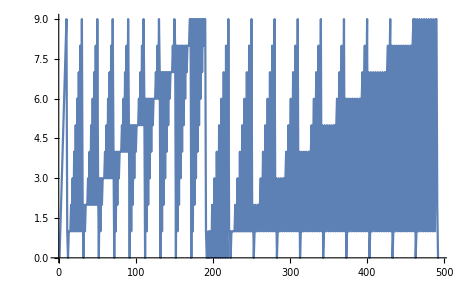
| Expected output: |  
  | -Graphics- |

Efectúe 4 pasos del análogo “esponja de Menger” del patrón de Sierpinski fractal del texto, pero con un kernel de la forma {{#,#,#},{#,0,#},{#,#,#}}. »


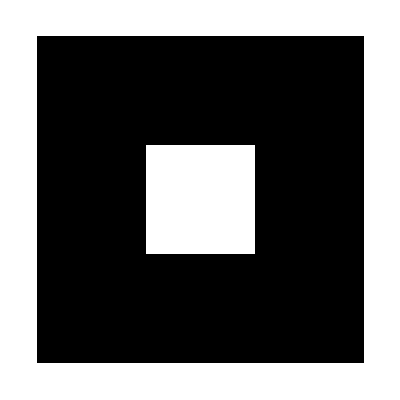
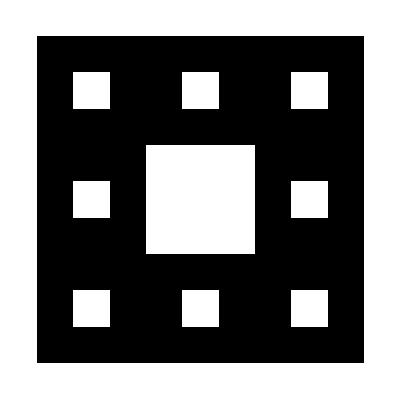
| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

Encuentre las ternas pitagóricas que tengan solo enteros, seleccionando {x,y,Sqrt[x^2+y^2]}, con x y y del 1 hasta el 20. »

| Expected output: |  
  | {{3,4,5},{4,3,5},{5,12,13},{6,8,10},{8,6,10},{8,15,17},{9,12,15},{12,5,13},{12,9,15},{12,16,20},{15,8,17},{15,20,25},{16,12,20},{20,15,25}} |

Encuentre las longitudes más largas entre las secuencias de dígitos idénticos en 2^n, con n hasta 100. »

| Expected output: |  
  | {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,1,1,1,2,3,2,2,2,1,1,1,1,1,2,1,1,1,1,2,3,3,4,3,3,3,3,2,2,1,2,3,2,2,2,1,1,1,2,2,2,2,2,2,2,2,2,1,1,1,1,2,2,2,3,3,3,3,3,2,2,1,2,2,3,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2} |

Tome los nombres de los enteros hasta el 100, y agrúpelos en sublistas con acuerdo a sus letras iniciales. »

| Expected output: |  
  | {{"one","one hundred"},{"two","three","ten","twelve","thirteen","twenty","twenty-one","twenty-two","twenty-three","twenty-four","twenty-five","twenty-six","twenty-seven","twenty-eight","twenty-nine","thirty","thirty-one","thirty-two","thirty-three","thirty-four","thirty-five","thirty-six","thirty-seven","thirty-eight","thirty-nine"},{"four","five","fourteen","fifteen","forty","forty-one","forty-two","forty-three","forty-four","forty-five","forty-six","forty-seven","forty-eight","forty-nine","fifty","fifty-one","fifty-two","fifty-three","fifty-four","fifty-five","fifty-six","fifty-seven","fifty-eight","fifty-nine"},{"six","seven","sixteen","seventeen","sixty","sixty-one","sixty-two","sixty-three","sixty-four","sixty-five","sixty-six","sixty-seven","sixty-eight","sixty-nine","seventy","seventy-one","seventy-two","seventy-three","seventy-four","seventy-five","seventy-six","seventy-seven","seventy-eight","seventy-nine"},{"eight","eleven","eighteen","eighty","eighty-one","eighty-two","eighty-three","eighty-four","eighty-five","eighty-six","eighty-seven","eighty-eight","eighty-nine"},{"nine","nineteen","ninety","ninety-one","ninety-two","ninety-three","ninety-four","ninety-five","ninety-six","ninety-seven","ninety-eight","ninety-nine"}} |

Ordene las 50 primeras palabras en WordList[ ] según la última letra. »

| Expected output: |  
  | {"a","abandoned","abashed","abbreviated","abed","abalone","abase","abate","abbe","abbreviate","abdicate","abeyance","abhorrence","abidance","abide","abducting","abiding","aah","abash","aardvark","aback","abdominal","abeam","abandon","abbreviation","abdication","abdomen","abduction","aberration","abjection","abattoir","abductor","abettor","abhor","abacus","abbess","abaft","abandonment","abasement","abashment","abatement","abbot","abduct","aberrant","abet","abhorrent","abject","abbey","ability","abjectly"} |

Haga una lista de los 20 primeros cuadrados, ordenada por sus primeros dígitos. »

| Expected output: |  
  | {1,16,100,121,144,169,196,25,225,256,289,36,324,361,4,49,400,64,81,9} |

Ordene los enteros hasta el 20, según las longitudes de sus nombres en inglés. »

| Expected output: |  
  | {1,2,6,10,4,5,9,3,7,8,11,12,20,15,16,13,14,18,19,17} |

Obtenga una muestra aleatoria de 20 palabras de WordList[ ], y agrúpelas en sublistas, de acuerdo con el número de sus caracteres. »

| Sample expected output: |  
  | {{"paste"},{"mistakenly","unintended","victorious","watercress"},{"powerful","jingoist","ballpark","rapeseed","dyslexia"},{"repeal"},{"paleontological"},{"encouragement"},{"countryside"},{"selfish","hedging"},{"barometer"},{"veil","well"},{"municipality"}} |

Encuentre las letras que aparecen en el alfabeto ucraniano, pero no en el ruso. »

| Expected output: |  
  | {"є","і","ї","ґ"} |

Use Intersection para encontrar los números que aparecen tanto en los 100 primeros cuadrados como en los 100 primeros cubos. »

| Expected output: |  
  | {1,64,729,4096} |

Encuentre la lista de los países que pertenecen tanto a la OTAN como al G8. »

| Expected output: |  
  | {"Canada","France","Germany","Italy","United Kingdom","United States"} |

Haga una rejilla donde aparezcan en columnas consecutivas todas las permutaciones posibles de los números 1 al 4. »

| Expected output: |  
  | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4
2 | 2 | 3 | 3 | 4 | 4 | 1 | 1 | 3 | 3 | 4 | 4 | 1 | 1 | 2 | 2 | 4 | 4 | 1 | 1 | 2 | 2 | 3 | 3
3 | 4 | 2 | 4 | 2 | 3 | 3 | 4 | 1 | 4 | 1 | 3 | 2 | 4 | 1 | 4 | 1 | 2 | 2 | 3 | 1 | 3 | 1 | 2
4 | 3 | 4 | 2 | 3 | 2 | 4 | 3 | 4 | 1 | 3 | 1 | 4 | 2 | 4 | 1 | 2 | 1 | 3 | 2 | 3 | 1 | 2 | 1 |

Haga una lista de todas las diferentes cadenas de caracteres que pueden obtenerse permutando los caracteres en “hello”. »

| Expected output: |  
  | {"ehllo","ehlol","eholl","elhlo","elhol","ellho","elloh","elohl","elolh","eohll","eolhl","eollh","hello","helol","heoll","hlelo","hleol","hlleo","hlloe","hloel","hlole","hoell","holel","holle","lehlo","lehol","lelho","leloh","leohl","leolh","lhelo","lheol","lhleo","lhloe","lhoel","lhole","lleho","lleoh","llheo","llhoe","lloeh","llohe","loehl","loelh","lohel","lohle","loleh","lolhe","oehll","oelhl","oellh","ohell","ohlel","ohlle","olehl","olelh","olhel","olhle","olleh","ollhe"} |

Obtenga un gráfico de arreglo de la secuencia de tuplas de tamaño 5, con el 0 y el 1. »

| Expected output: |  
  |  |

Genere una lista de 10 secuencias aleatorias de 5 letras del alfabeto inglés. »

| Sample expected output: |  
  | {"ayasl","icnry","ahbaa","jqkpc","orlaf","rmexo","ngrfy","vwhii","wjiqn","gngvk"} |

Encuentre una forma más sencilla para Flatten[Table[{i,j,k},{i,2},{j,2},{k,2}],2]. »

| Expected output: |  
  | {{1,1,1},{1,1,2},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}} |

Produzca un gráfico de arreglo con los números de las letras en los 1000 primeros caracteres del artículo “computers” en Wikipedia, con 30 letras en cada renglón. »

| Expected output: |  
  | -Graphics- |

Agrupe los enteros hasta el 30 en listas basadas en sus valores módulo 3. »

| Expected output: |  
  | {{1,4,7,10,13,16,19,22,25,28},{2,5,8,11,14,17,20,23,26,29},{3,6,9,12,15,18,21,24,27,30}} |

Agrupe las 50 primeras potencias de 2 de acuerdo con el valor de sus últimos dígitos. »

| Expected output: |  
  | {{2,32,512,8192,131072,2097152,33554432,536870912,8589934592,137438953472,2199023255552,35184372088832,562949953421312},{4,64,1024,16384,262144,4194304,67108864,1073741824,17179869184,274877906944,4398046511104,70368744177664,1125899906842624},{8,128,2048,32768,524288,8388608,134217728,2147483648,34359738368,549755813888,8796093022208,140737488355328},{16,256,4096,65536,1048576,16777216,268435456,4294967296,68719476736,1099511627776,17592186044416,281474976710656}} |

Obtenga un gráfico con los puntos unidos con el resultado de ordenar los números del −10 al +10, según sus valores absolutos. »

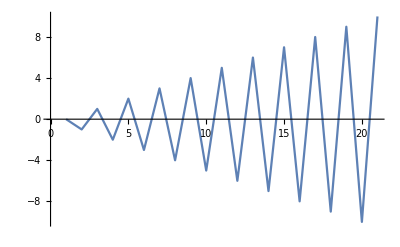
| Expected output: |  
  | -Graphics- |

Produzca un gráfico con los puntos unidos de los 200 primeros cuadrados, ordenados por sus dígitos iniciales. »

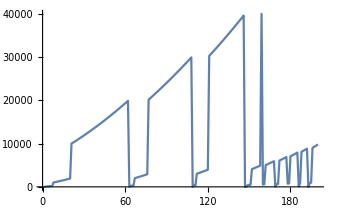
| Expected output: |  
  | -Graphics- |

Produzca el gráfico con los puntos unidos de los enteros hasta el 200, ordenados según las longitudes de sus nombres en inglés. »

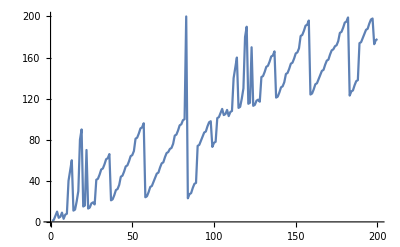
| Expected output: |  
  | -Graphics- |

Obtenga una muestra aleatoria de 25 palabras de WordList[]. »

| Expected output: |  
  | {"autopsy","reclassification","advancement","forswear","swimwear","cravat","cyclone","taps","diplomatic","effacement","peaked","ponderously","publication","immune","outstay","petrol","deaf","bilk","oddments","scoreboard","lifeless","debriefing","radiogram","doting","inter"} |

Intercale puntos en la cadena de caracteres “UNCLE” para obtener“U.N.C.L.E.”. »

| Expected output: |  
  | "U.N.C.L.E." |

Encuentre las letras que aparecen en sueco o en polaco, pero no en inglés. »

| Expected output: |  
  | {"ą","ę","ń","ś","ź","ż","å","ä","ć","ł","ó","ö"} |

Encuentre los países que pertenecen a la World Health Organization pero no a las Naciones Unidas. »

| Expected output: |  
  | {"Cook Islands","Niue"} |

Haga la lista de todas las mezclas de dos de los colores rojo, verde y azul. »

| Expected output: |  
  | {RGBColor[1, 0, 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[0, 1, 0],RGBColor[0, Rational[1, 2], Rational[1, 2]],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[0, Rational[1, 2], Rational[1, 2]],RGBColor[0, 0, 1]} |

Haga una lista de gráficos de arreglo, cada uno con 50 renglones y tamaño de imagen 50, de las tuplas sucesivas de tamaño 8, con el 0 y el 1. »

| Expected output: |  
  | {,,,,} |

Genere 1000 secuencias aleatorias de 4 letras, y hacer la lista de aquellas que aparezcan en WordList[ ].  »

| Expected output: |  
  | {"avow","frog","know","lido","snot"} |

Preguntas y respuestas

¿Cómo funciona Partition cuando los bloques no encajan perfectamente?

A menos que se indique lo contrario, solo se incluirán bloques completos, de tal modo que se eliminarán aquellos elementos que aparezcan solo en bloques incompletos. Sin embargo, si se dice, por ejemplo, Partition[lista,UpTo[4]], se harán bloques hasta de longitud 4, y el último de ellos podría ser más corto si fuera necesario.

Notas técnicas

Transpose puede verse como la transposición de filas y columnas en una matriz.

ArrayFlatten aplana un arreglo de arreglos para dejar un solo arreglo o, alternativamente, para dejar una matriz de matrices en una sola matriz.

DeleteDuplicates[lista] hace lo mismo que Union[lista], salvo que no reordena los elementos.

Para explorar más

Guía para reorganizar y reestructurar listas en Wolfram Language »